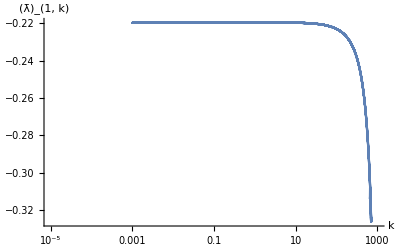

```mathematica
SetDirectory[NotebookDirectory[]];
k=Flatten[Import["./k1.dat"]]/197.33;
lam1=Flatten[Import["./lam1.dat"]];
lam2=Flatten[Import["./lam2.dat"]];
lam1dl=lam1[[1;;Length[k]]]*k^-2;
lam2dl=lam2[[1;;Length[k]]];
plotl1=ListLinePlot[Transpose[{k*197.33,lam1dl}],PlotRange->{{10^-5,1000},All},ScalingFunctions->{"Log",Automatic},AxesLabel->{"k","(λ̄)_(1, k)"}]
```

```mathematica
lam1dl[[-1]]
```

234852.

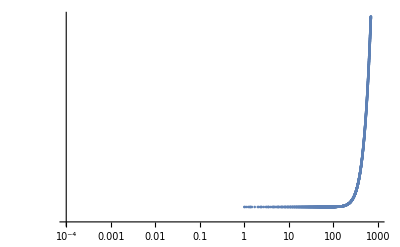

```mathematica
ListPlot[Transpose[{k*197.33,lam2dl}],PlotRange->{{10^-4,1000},All},ScalingFunctions->{"Log","Log"}]
```

```mathematica
ListPlot[Transpose[{k*197.33,lam2}],PlotRange->{{10^-4,1000},All},ScalingFunctions->{"Log","Log"}]
```

-Graphics-

```mathematica
T=Flatten[Import["./TMeV.dat"]];
sigma=Flatten[Import["./fpi.dat"]];
mp=Flatten[Import["./mPion.dat"]];
```

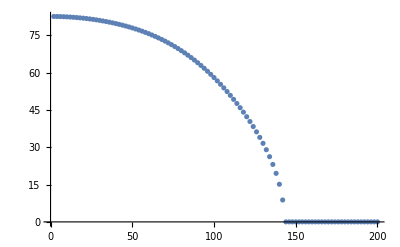

```mathematica
ListPlot[Transpose[{T,sigma}]]
```

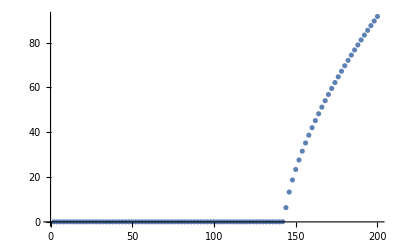

```mathematica
ListPlot[Transpose[{T,mp}]]
```

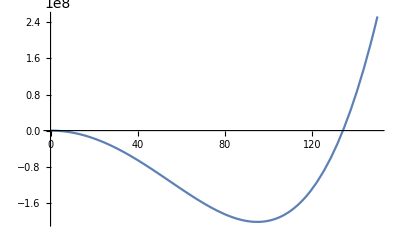

```mathematica
Plot[((sigma^2/2)^2*20)/2-300^2(sigma^2/2),{sigma,0,150}]
```